{-40,-20,0,10,70,100,120}

{1250,1280,1800,1350,1480,1580,1700}

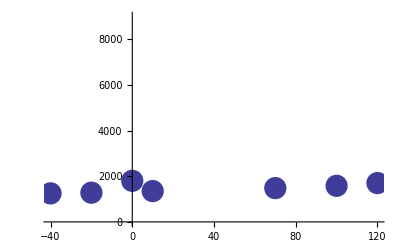

(1 | -40 | 1600 | -64000 | 2560000 | -102400000 | 4096000000 | 1250
1 | -20 | 400 | -8000 | 160000 | -3200000 | 64000000 | 1280
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1800
1 | 10 | 100 | 1000 | 10000 | 100000 | 1000000 | 1350
1 | 70 | 4900 | 343000 | 24010000 | 1680700000 | 117649000000 | 1480
1 | 100 | 10000 | 1000000 | 100000000 | 10000000000 | 1000000000000 | 1580
1 | 120 | 14400 | 1728000 | 207360000 | 24883200000 | 2985984000000 | 1700)

1800-(376469 x)/15120-(48135209 x^2)/19958400+(6491179 x^3)/199584000+(352189 x^4)/380160000-(337933 x^5)/19958400000+(1609 x^6)/22809600000

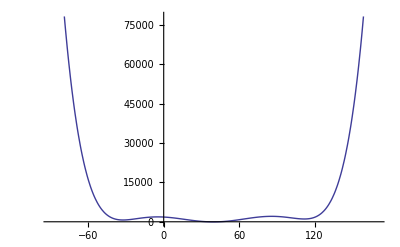

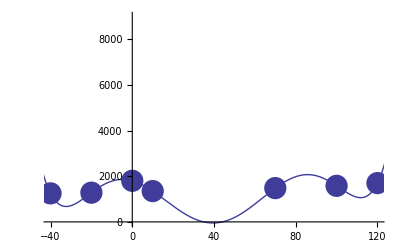

```mathematica
n=Input["Dame el número de puntos"];
MatrizX={};
MatrizY={};

For[i=1,i≤n,i++,
VariableX=Input["Introduzca X"];
AppendTo[MatrizX,VariableX];
VariableY=Input["Introduzca Y"];
AppendTo[MatrizY,VariableY];
];

MatrizX
MatrizY
Experimento=Table[{MatrizX[[i]],MatrizY[[i]]},{i,1,n}];
grafica=ListPlot[Experimento,PlotStyle->PointSize[0.04],PlotRange->{{-40,120},{0,9000}}]
MatrizC={};
MatrizS={};

For[i=1,i≤n,i++,
Renglon={};
For[j=1,j≤n,j++,
If[(MatrizX[[i]]==0 && (j-1)==0),Dato=1,Dato=MatrizX[[i]]^(j-1) ];
AppendTo[Renglon,Dato]
];
AppendTo[Renglon,MatrizY[[i]]];
AppendTo[MatrizC,Renglon]
]
MatrizC//MatrixForm

For[i=1,i≤n,i++,
AppendTo[MatrizS,0]
]

For[k=1,k≤n,k++,
(*Aqui iria intercambio*)
For[i=k+1,i≤n,i++,
factor=MatrizC[[i,k]]/MatrizC[[k,k]];
For[j=1,j≤n+1,j++,
MatrizC[[i,j]]=MatrizC[[i,j]]-MatrizC[[k,j]]*factor
]
]
]
MatrizS[[n]]=MatrizC[[n,n+1]]/MatrizC[[n,n]];
For[i=n-1,i≥1,i--,
suma=0;
For[j=n,j≥i+1,j--,
suma =suma+MatrizS[[j]]*MatrizC[[i,j]]
];
MatrizS[[i]]=(MatrizC[[i,n+1]]-suma)/MatrizC[[i,i]]
]

Suma=0;
For[i=0,i≤ n-1,i++,
Suma=Suma+MatrizS[[i+1]] x^i
];

pol[x_]=Suma
grafica2=Plot[pol[x],{x,MatrizX[[1]]-50,MatrizX[[n]]+50}]
Show[grafica,grafica2]
```

```mathematica
pol[-40]//N
```

1250.